-(9 ⅇ^(-3 π/2) (-333+333 ⅇ^(3 π/2)-250 π) Cos[x])/625000

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→-1.59094},{y→0.}}

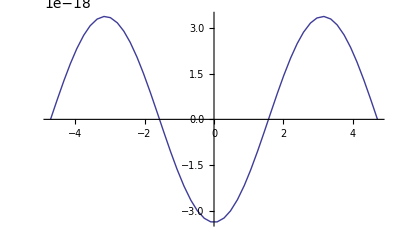

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(* Solution of the Reissner-Mindlin model with boundary layer of the semi-infinite plate problem *)
(* Input parameter *)
Clear All;
Q=1; (* Load *)
L=1; (* Length of plate along x-axis *)
Y = 2*10^7; (* Young's modulus *)
ν = 3; (* Poisson ratio *)
d=1/10; (* Thickness of plate *)
κ=5 /6; (* Shear factor *)
M = (Y*d^3)/(12(1-ν^2)); (* Plate constant *)
G=Y/(2(1+ν)); (* Shear modulus *)

γ=√(12κ+(d/L)^2);
c1=-d^3/(M*L^2);
c2=-d^3/(2M*L^2);
c3=0;
c4=0;
βx[x_,y_]:=(Q*L^5)/d^3(-d^3/(M*L^2)-c1*Exp[-y/L]-c2*y/L*Exp[-y/L]+c3*(d^2*Exp[-y/L])/(κ*G*L^4)-c4*(γ*d*Exp[γ*-y/d])/(κ*G*L^3))*Sin[x/L];
βy[x_,y_]:=(Q*L^5)/d^3(-c1*Exp[-y/L]+c2*(1-y/L)*Exp[-y/L]+c3*(d^2*Exp[-y/L])/(κ*G*L^4)-c4*(d^2*Exp[γ*-y/d])/(κ*G*L^4))*Cos[x/L];
w[x_,y_]:=L*((Q*L^5)/d^3(d^3/(M*L^2)+d^2/(κ*G*L^4)+c1*Exp[-y/L]+c2((2*M)/(κ*G*L^2*d)+y/L)*Exp[-y/L]-c3*(d^2*Exp[-y/L])/(κ*G*L^4))*Cos[x/L]);
Print[Simplify[w[x,3/2*Pi]]]
Print[NSolve[w[0,y]==0,{y}]]
Plot[w[x,-1.590939063264682],{x,-L*3/2*Pi,L*3/2*Pi}]
Plot3D[βx[x,y],{x,-L*3/2*Pi,L*3/2*Pi},{y,-1.590939063264682,0}]
Plot3D[βy[x,y],{x,-L*3/2*Pi,L*3/2*Pi},{y,-1.590939063264682,0}]
Plot3D[w[x,y],{x,-L*3/2*Pi,L*3/2*Pi},{y,-1.590939063264682,0}]
```

```mathematica
Simplify[2423/1523-1.590939063264682]
```

-1.26955×10^-7